```mathematica
(* local Weyl operators *)
Clear[v,u,p,n]
p=5;
ω=ⅇ^(ⅈ*(2π)/p);
v = ConstantArray[0,{p,p}];
u = ConstantArray[0,{p,p}];
Do[
If[n+1≤p,
v[[n,n+1]]=1;
,
v[[p,1]]=1;
];
u[[n,n]]=ω^(n-1)
,{n,p}];
v=SparseArray[v];
u=SparseArray[u];
MatrixForm[v]
MatrixForm[u]
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0
0 | ⅇ^((2 ⅈ π)/5) | 0 | 0 | 0
0 | 0 | ⅇ^((4 ⅈ π)/5) | 0 | 0
0 | 0 | 0 | ⅇ^(-(4 ⅈ π)/5) | 0
0 | 0 | 0 | 0 | ⅇ^(-(2 ⅈ π)/5))

```mathematica
Clear[linkVals]
linkVals[ϕ_] = Refine[Eigenvalues[ⅇ^(ⅈ ϕ)*v.(v.u)†+ⅇ^(-ⅈ ϕ)*(v.u).v†],ϕ>0]//FullSimplify
```

{2 Cos[ϕ],(-1)^(1/5) ⅇ^(-ⅈ ϕ) ((-1)^(3/5)-ⅇ^(2 ⅈ ϕ)),-(-1)^(3/5) ⅇ^(-ⅈ ϕ) ((-1)^(4/5)+ⅇ^(2 ⅈ ϕ)),(-1)^(1/5) ⅇ^(-ⅈ ϕ) (-1+(-1)^(3/5) ⅇ^(2 ⅈ ϕ)),(-1)^(2/5) ⅇ^(-ⅈ ϕ) (-(-1)^(1/5)+ⅇ^(2 ⅈ ϕ))}

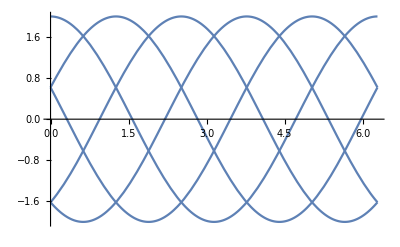

```mathematica
Plot[linkVals[ϕ],{ϕ,0,2π}]
```

```mathematica
(* give them a string for nonlocal commutation relations *)
Clear[L,V,U]
L=3;
Do[
V[i]=KroneckerProduct[IdentityMatrix[p^(i-1)],v,IdentityMatrix[p^(L-i)]];
U[i]=KroneckerProduct[IdentityMatrix[p^(i-1)],u,IdentityMatrix[p^(L-i)]];

Γ[i]=If[i>1,V[i].∏_(j=1)^(i-1) U[j],V[i]];
Δ[i]=Γ[i].U[i];

,{i,1,L}];
```

```mathematica
spectrum={};
ϕs={};
Do[
h=0.0;
J=1*ⅇ^(ⅈ ϕ);
HVP = -h*(∑_(i=1)^L Γ[i]†.Δ[i])-J*(∑_(i=1)^(L-1) Δ[i].Γ[i+1]†);
HVP=HVP+HVP†;
{evals,evecs}=Eigensystem[Normal[HVP]];
evals=Tally[evals/Max[(L-1),1],Abs[#1-#2]<10^-6&];
AppendTo[spectrum,evals];
AppendTo[ϕs,ϕ/π];
,{ϕ,π/31,2π,π/33}]
```

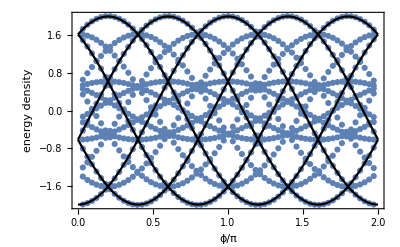

```mathematica
min=Min[Table[Length@ss,{ss,spectrum}]];
pmax=Max[Partition[Flatten[spectrum],2][[All,1]]];
pmin=Min[Partition[Flatten[spectrum],2][[All,1]]];
Show[Table[{ϕs,spectrum[[All,i,1]]}ᵀ//ListPlot,{i,min}],Plot[Table[-2Re[J] Cos[π(x-2n/p)],{n,0,p-1}],{x,0,2},PlotStyle->Black],PlotRange->{pmin,pmax},GridLines->{Table[i/p,{i,2p}],{}},Frame->True,FrameLabel->{"ϕ/π","energy density"}]
```

```mathematica
(* check all local commutation relations *)
test={};
Do[
tp=SparseArray[Γ[i].Γ[j]-ω*Γ[j].Γ[i]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

tp=SparseArray[Γ[j].Γ[i]-ω**Γ[i].Γ[j]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

tp=SparseArray[Δ[i].Δ[j]-ω*Δ[j].Δ[i]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

tp=SparseArray[Δ[j].Δ[i]-ω**Δ[i].Δ[j]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

,{j,L},{i,j-1}]
Do[
tp=SparseArray[Γ[i].Δ[j]-ω*Δ[j].Γ[i]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];
,{j,L},{i,j}];
test
```

{}

```mathematica
(* local Weyl operators *)
Clear[v,u,p,n]
p=3;
ω=ⅇ^(ⅈ*(2π)/p);
v = ConstantArray[0,{p,p}];
u = ConstantArray[0,{p,p}];
Do[
If[n+1≤p,
v[[n,n+1]]=1;
,
v[[p,1]]=1;
];
u[[n,n]]=ω^(n-1)
,{n,p}];
v=SparseArray[v];
u=SparseArray[u];
MatrixForm[v];
MatrixForm[u];
(* give them a string for nonlocal commutation relations *)
Clear[L,V,U];
L=2;
Do[
V[i]=KroneckerProduct[IdentityMatrix[p^(i-1)],v,IdentityMatrix[p^(L-i)]];
U[i]=KroneckerProduct[IdentityMatrix[p^(i-1)],u,IdentityMatrix[p^(L-i)]];

Γ[i]=If[i>1,V[i].∏_(j=1)^(i-1) U[j],V[i]];
Δ[i]=Γ[i].U[i];

,{i,1,L}];
```

```mathematica
spectrum={};
ϕs={};
Do[
HSQ=ConstantArray[0,Dimensions[Γ[1]]];
HSQ = ⅇ^(ⅈ ϕ)(Γ[1].Δ[1]†+Γ[2].Δ[2]†);
HSQ += ⅇ^(ⅈ ϕ)(Δ[1].Γ[2]†+Δ[2].Γ[1]†);
HSQ=HSQ+HSQ†;
{evals,evecs}=Eigensystem[Normal[N[HSQ]]];
evals=Tally[evals/4//Sort,Abs[#1-#2]<10^-6&];
AppendTo[spectrum,evals];
AppendTo[ϕs,ϕ/π];
,{ϕ,π/31,2π,π/33}]
```

```mathematica
spectrum[[1]]
```

{{-1.60615,2},{-1.36201,2},{-0.98184,2},{-0.912342,2},{-0.83783,2},{-0.559709,2},{-0.503163,2},{-0.41098,2},{-0.328029,2},{-0.318203,2},{-0.236322,2},{-0.160147,2},{-0.132609,2},{-0.109616,2},{-0.100155,2},{-0.0388942,2},{0.0388942,2},{0.100155,2},{0.109616,2},{0.132609,2},{0.160147,2},{0.236322,2},{0.318203,2},{0.328029,2},{0.41098,2},{0.503163,2},{0.559709,2},{0.83783,2},{0.912342,2},{0.98184,2},{1.36201,2},{1.60615,2}}

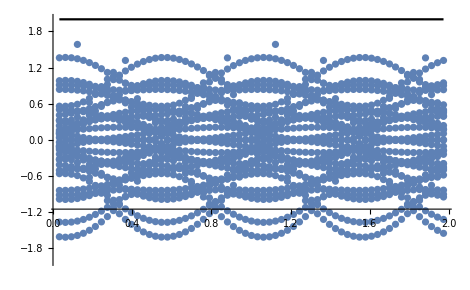

```mathematica
min=Min[Table[Length@ss,{ss,spectrum}]];
pmax=Max[Partition[Flatten[spectrum],2][[All,1]]];
pmin=Min[Partition[Flatten[spectrum],2][[All,1]]];
Show[Table[{ϕs,spectrum[[All,i,1]]}ᵀ//ListPlot,{i,min}],ListPlot[{ϕs,spectrum[[All,2,2]]}ᵀ,PlotStyle->Black,Joined->True],FrameLabel->{"ϕ/π","energy density"},PlotStyle->Black,PlotRange->{-2,2}]
```

```mathematica
spectrum={};
ϕs={};
Do[
HSQ=ConstantArray[0,Dimensions[Γ[1]]];
HSQ = ⅇ^(ⅈ ϕ)(Γ[1].Γ[2]†+Γ[2].Δ[2]†);
HSQ += ⅇ^(ⅈ ϕ)(Δ[2].Δ[1]†+Δ[1].Γ[1]†);
HSQ=HSQ+HSQ†;
{evals,evecs}=Eigensystem[Normal[N[HSQ]]];
evals=Tally[evals/4//Sort,Abs[#1-#2]<10^-6&];
AppendTo[spectrum,evals];
AppendTo[ϕs,ϕ/π];
,{ϕ,0,2π,π/33}]
```

```mathematica
spectrum
```

{{{-1.32364,1},{-1.1691,2},{-0.777351,2},{-0.401639,2},{-0.364121,1},{-0.302264,2},{0.0377618,1},{0.0911135,2},{0.122842,2},{0.206773,2},{0.253915,2},{0.323639,1},{0.802233,2},{1.17348,2},{1.32636,1}},{{-1.32079,1},{-1.16442,2},{-0.776155,2},{-0.401683,2},{-0.361243,1},{-0.324709,2},{-0.0000303852,1},{0.104213,2},{0.11171,2},{0.20714,2},{0.274356,2},{0.361275,1},{0.799269,2},{1.17028,2},{1.32079,1}},{{-1.31241,1},{-1.15049,2},{-0.772655,2},{-0.401961,2},{-0.380649,2},{-0.352629,1},{-0.0815121,1},{0.0664256,2},{0.157236,2},{0.213032,2},{0.317764,2},{0.442353,1},{0.790427,2},{1.16088,2},{1.30419,1}},{{-1.29895,1},{-1.12763,2},{-0.767114,2},{-0.452583,2},{-0.40289,2},{-0.338342,1},{-0.175355,1},{0.0263197,2},{0.180945,2},{0.253452,2},{0.367826,2},{0.535728,1},{0.775858,2},{1.14582,2},{1.27692,1}},{{-1.28126,1},{-1.09648,2},{-0.760002,2},{-0.529827,2},{-0.405046,2},{-0.318485,1},{-0.270167,1},{-0.00992787,2},{0.179412,2},{0.320738,2},{0.41914,2},{0.630261,1},{0.755835,2},{1.12616,2},{1.23965,1}},{{-1.26067,1},{-1.05824,2},{-0.752029,2},{-0.606311,2},{-0.40891,2},{-0.360688,1},{-0.293207,1},{-0.0392883,2},{0.171979,2},{0.388993,2},{0.469427,2},{0.720799,1},{0.7308,2},{1.10358,2},{1.19377,1}},{{-1.23917,1},{-1.01551,2},{-0.744185,2},{-0.677014,2},{-0.443036,1},{-0.414441,2},{-0.262702,1},{-0.0600194,2},{0.161723,2},{0.450107,2},{0.517109,2},{0.701536,2},{0.802439,1},{1.0807,2},{1.14247,1}},{{-1.21955,1},{-0.975029,2},{-0.737729,2},{-0.733938,2},{-0.513316,1},{-0.420659,2},{-0.227219,1},{-0.0715336,2},{0.149299,2},{0.498452,2},{0.559915,2},{0.670007,2},{0.864722,1},{1.06122,2},{1.09537,1}},{{-1.20538,1},{-0.954607,2},{-0.758668,2},{-0.73405,2},{-0.567269,1},{-0.425636,2},{-0.187068,1},{-0.0743951,2},{0.134968,2},{0.528695,2},{0.587698,2},{0.646382,2},{0.879795,1},{1.04961,2},{1.07992,1}},{{-1.20031,1},{-0.97176,2},{-0.734294,2},{-0.733556,2},{-0.600825,1},{-0.427127,2},{-0.142649,1},{-0.0700267,2},{0.118891,2},{0.53695,2},{0.571185,2},{0.660263,2},{0.832636,1},{1.04947,2},{1.11114,1}},{{-1.20642,1},{-1.01035,2},{-0.73886,2},{-0.675026,2},{-0.611683,1},{-0.423543,2},{-0.094496,1},{-0.0602799,2},{0.101216,2},{0.523027,2},{0.532867,2},{0.689816,2},{0.753275,1},{1.06113,2},{1.15933,1}},{{-1.22273,1},{-1.05214,2},{-0.747111,2},{-0.602066,2},{-0.600813,1},{-0.414592,2},{-0.0471483,2},{-0.0433834,1},{0.0821234,2},{0.490811,2},{0.490879,2},{0.660184,1},{0.717971,2},{1.08127,2},{1.20674,1}},{{-1.24553,1},{-1.09018,2},{-0.757601,2},{-0.572072,1},{-0.523044,2},{-0.401244,2},{-0.0326907,2},{0.00937407,1},{0.0619228,2},{0.446172,2},{0.449436,2},{0.560263,1},{0.7421,2},{1.10513,2},{1.24796,1}},{{-1.27028,1},{-1.12187,2},{-0.768594,2},{-0.530342,1},{-0.44307,2},{-0.385298,2},{-0.0190499,2},{0.0412748,2},{0.0609428,1},{0.395159,2},{0.411433,2},{0.458655,1},{0.76151,2},{1.1285,2},{1.28103,1}},{{-1.2931,1},{-1.14607,2},{-0.77848,2},{-0.480155,1},{-0.369041,2},{-0.367866,2},{-0.00833608,2},{0.0217339,2},{0.102835,1},{0.34382,2},{0.365299,1},{0.379897,2},{0.77596,2},{1.14838,2},{1.30512,1}},{{-1.3111,1},{-1.16227,2},{-0.785954,2},{-0.425505,1},{-0.355152,2},{-0.306331,2},{-0.0020647,2},{0.00665851,2},{0.106038,1},{0.299188,2},{0.310631,1},{0.357751,2},{0.785419,2},{1.16276,2},{1.31994,1}},{{-1.32234,1},{-1.17031,2},{-0.790032,2},{-0.370748,1},{-0.346689,2},{-0.271243,2},{-0.0000823433,2},{0.000311727,2},{0.0434927,1},{0.270913,2},{0.324051,1},{0.346791,2},{0.790013,2},{1.17033,2},{1.32554,1}},{{-1.32554,1},{-1.17033,2},{-0.790013,2},{-0.346791,2},{-0.324051,1},{-0.270913,2},{-0.0434927,1},{-0.000311727,2},{0.0000823433,2},{0.271243,2},{0.346689,2},{0.370748,1},{0.790032,2},{1.17031,2},{1.32234,1}},{{-1.31994,1},{-1.16276,2},{-0.785419,2},{-0.357751,2},{-0.310631,1},{-0.299188,2},{-0.106038,1},{-0.00665851,2},{0.0020647,2},{0.306331,2},{0.355152,2},{0.425505,1},{0.785954,2},{1.16227,2},{1.3111,1}},{{-1.30512,1},{-1.14838,2},{-0.77596,2},{-0.379897,2},{-0.365299,1},{-0.34382,2},{-0.102835,1},{-0.0217339,2},{0.00833608,2},{0.367866,2},{0.369041,2},{0.480155,1},{0.77848,2},{1.14607,2},{1.2931,1}},{{-1.28103,1},{-1.1285,2},{-0.76151,2},{-0.458655,1},{-0.411433,2},{-0.395159,2},{-0.0609428,1},{-0.0412748,2},{0.0190499,2},{0.385298,2},{0.44307,2},{0.530342,1},{0.768594,2},{1.12187,2},{1.27028,1}},{{-1.24796,1},{-1.10513,2},{-0.7421,2},{-0.560263,1},{-0.449436,2},{-0.446172,2},{-0.0619228,2},{-0.00937407,1},{0.0326907,2},{0.401244,2},{0.523044,2},{0.572072,1},{0.757601,2},{1.09018,2},{1.24553,1}},{{-1.20674,1},{-1.08127,2},{-0.717971,2},{-0.660184,1},{-0.490879,2},{-0.490811,2},{-0.0821234,2},{0.0433834,1},{0.0471483,2},{0.414592,2},{0.600813,1},{0.602066,2},{0.747111,2},{1.05214,2},{1.22273,1}},{{-1.15933,1},{-1.06113,2},{-0.753275,1},{-0.689816,2},{-0.532867,2},{-0.523027,2},{-0.101216,2},{0.0602799,2},{0.094496,1},{0.423543,2},{0.611683,1},{0.675026,2},{0.73886,2},{1.01035,2},{1.20642,1}},{{-1.11114,1},{-1.04947,2},{-0.832636,1},{-0.660263,2},{-0.571185,2},{-0.53695,2},{-0.118891,2},{0.0700267,2},{0.142649,1},{0.427127,2},{0.600825,1},{0.733556,2},{0.734294,2},{0.97176,2},{1.20031,1}},{{-1.07992,1},{-1.04961,2},{-0.879795,1},{-0.646382,2},{-0.587698,2},{-0.528695,2},{-0.134968,2},{0.0743951,2},{0.187068,1},{0.425636,2},{0.567269,1},{0.73405,2},{0.758668,2},{0.954607,2},{1.20538,1}},{{-1.09537,1},{-1.06122,2},{-0.864722,1},{-0.670007,2},{-0.559915,2},{-0.498452,2},{-0.149299,2},{0.0715336,2},{0.227219,1},{0.420659,2},{0.513316,1},{0.733938,2},{0.737729,2},{0.975029,2},{1.21955,1}},{{-1.14247,1},{-1.0807,2},{-0.802439,1},{-0.701536,2},{-0.517109,2},{-0.450107,2},{-0.161723,2},{0.0600194,2},{0.262702,1},{0.414441,2},{0.443036,1},{0.677014,2},{0.744185,2},{1.01551,2},{1.23917,1}},{{-1.19377,1},{-1.10358,2},{-0.7308,2},{-0.720799,1},{-0.469427,2},{-0.388993,2},{-0.171979,2},{0.0392883,2},{0.293207,1},{0.360688,1},{0.40891,2},{0.606311,2},{0.752029,2},{1.05824,2},{1.26067,1}},{{-1.23965,1},{-1.12616,2},{-0.755835,2},{-0.630261,1},{-0.41914,2},{-0.320738,2},{-0.179412,2},{0.00992787,2},{0.270167,1},{0.318485,1},{0.405046,2},{0.529827,2},{0.760002,2},{1.09648,2},{1.28126,1}},{{-1.27692,1},{-1.14582,2},{-0.775858,2},{-0.535728,1},{-0.367826,2},{-0.253452,2},{-0.180945,2},{-0.0263197,2},{0.175355,1},{0.338342,1},{0.40289,2},{0.452583,2},{0.767114,2},{1.12763,2},{1.29895,1}},{{-1.30419,1},{-1.16088,2},{-0.790427,2},{-0.442353,1},{-0.317764,2},{-0.213032,2},{-0.157236,2},{-0.0664256,2},{0.0815121,1},{0.352629,1},{0.380649,2},{0.401961,2},{0.772655,2},{1.15049,2},{1.31241,1}},{{-1.32079,1},{-1.17028,2},{-0.799269,2},{-0.361275,1},{-0.274356,2},{-0.20714,2},{-0.11171,2},{-0.104213,2},{0.0000303852,1},{0.324709,2},{0.361243,1},{0.401683,2},{0.776155,2},{1.16442,2},{1.32079,1}},{{-1.32636,1},{-1.17348,2},{-0.802233,2},{-0.323639,1},{-0.253915,2},{-0.206773,2},{-0.122842,2},{-0.0911135,2},{-0.0377618,1},{0.302264,2},{0.364121,1},{0.401639,2},{0.777351,2},{1.1691,2},{1.32364,1}},{{-1.32079,1},{-1.17028,2},{-0.799269,2},{-0.361275,1},{-0.274356,2},{-0.20714,2},{-0.11171,2},{-0.104213,2},{0.0000303852,1},{0.324709,2},{0.361243,1},{0.401683,2},{0.776155,2},{1.16442,2},{1.32079,1}},{{-1.30419,1},{-1.16088,2},{-0.790427,2},{-0.442353,1},{-0.317764,2},{-0.213032,2},{-0.157236,2},{-0.0664256,2},{0.0815121,1},{0.352629,1},{0.380649,2},{0.401961,2},{0.772655,2},{1.15049,2},{1.31241,1}},{{-1.27692,1},{-1.14582,2},{-0.775858,2},{-0.535728,1},{-0.367826,2},{-0.253452,2},{-0.180945,2},{-0.0263197,2},{0.175355,1},{0.338342,1},{0.40289,2},{0.452583,2},{0.767114,2},{1.12763,2},{1.29895,1}},{{-1.23965,1},{-1.12616,2},{-0.755835,2},{-0.630261,1},{-0.41914,2},{-0.320738,2},{-0.179412,2},{0.00992787,2},{0.270167,1},{0.318485,1},{0.405046,2},{0.529827,2},{0.760002,2},{1.09648,2},{1.28126,1}},{{-1.19377,1},{-1.10358,2},{-0.7308,2},{-0.720799,1},{-0.469427,2},{-0.388993,2},{-0.171979,2},{0.0392883,2},{0.293207,1},{0.360688,1},{0.40891,2},{0.606311,2},{0.752029,2},{1.05824,2},{1.26067,1}},{{-1.14247,1},{-1.0807,2},{-0.802439,1},{-0.701536,2},{-0.517109,2},{-0.450107,2},{-0.161723,2},{0.0600194,2},{0.262702,1},{0.414441,2},{0.443036,1},{0.677014,2},{0.744185,2},{1.01551,2},{1.23917,1}},{{-1.09537,1},{-1.06122,2},{-0.864722,1},{-0.670007,2},{-0.559915,2},{-0.498452,2},{-0.149299,2},{0.0715336,2},{0.227219,1},{0.420659,2},{0.513316,1},{0.733938,2},{0.737729,2},{0.975029,2},{1.21955,1}},{{-1.07992,1},{-1.04961,2},{-0.879795,1},{-0.646382,2},{-0.587698,2},{-0.528695,2},{-0.134968,2},{0.0743951,2},{0.187068,1},{0.425636,2},{0.567269,1},{0.73405,2},{0.758668,2},{0.954607,2},{1.20538,1}},{{-1.11114,1},{-1.04947,2},{-0.832636,1},{-0.660263,2},{-0.571185,2},{-0.53695,2},{-0.118891,2},{0.0700267,2},{0.142649,1},{0.427127,2},{0.600825,1},{0.733556,2},{0.734294,2},{0.97176,2},{1.20031,1}},{{-1.15933,1},{-1.06113,2},{-0.753275,1},{-0.689816,2},{-0.532867,2},{-0.523027,2},{-0.101216,2},{0.0602799,2},{0.094496,1},{0.423543,2},{0.611683,1},{0.675026,2},{0.73886,2},{1.01035,2},{1.20642,1}},{{-1.20674,1},{-1.08127,2},{-0.717971,2},{-0.660184,1},{-0.490879,2},{-0.490811,2},{-0.0821234,2},{0.0433834,1},{0.0471483,2},{0.414592,2},{0.600813,1},{0.602066,2},{0.747111,2},{1.05214,2},{1.22273,1}},{{-1.24796,1},{-1.10513,2},{-0.7421,2},{-0.560263,1},{-0.449436,2},{-0.446172,2},{-0.0619228,2},{-0.00937407,1},{0.0326907,2},{0.401244,2},{0.523044,2},{0.572072,1},{0.757601,2},{1.09018,2},{1.24553,1}},{{-1.28103,1},{-1.1285,2},{-0.76151,2},{-0.458655,1},{-0.411433,2},{-0.395159,2},{-0.0609428,1},{-0.0412748,2},{0.0190499,2},{0.385298,2},{0.44307,2},{0.530342,1},{0.768594,2},{1.12187,2},{1.27028,1}},{{-1.30512,1},{-1.14838,2},{-0.77596,2},{-0.379897,2},{-0.365299,1},{-0.34382,2},{-0.102835,1},{-0.0217339,2},{0.00833608,2},{0.367866,2},{0.369041,2},{0.480155,1},{0.77848,2},{1.14607,2},{1.2931,1}},{{-1.31994,1},{-1.16276,2},{-0.785419,2},{-0.357751,2},{-0.310631,1},{-0.299188,2},{-0.106038,1},{-0.00665851,2},{0.0020647,2},{0.306331,2},{0.355152,2},{0.425505,1},{0.785954,2},{1.16227,2},{1.3111,1}},{{-1.32554,1},{-1.17033,2},{-0.790013,2},{-0.346791,2},{-0.324051,1},{-0.270913,2},{-0.0434927,1},{-0.000311727,2},{0.0000823433,2},{0.271243,2},{0.346689,2},{0.370748,1},{0.790032,2},{1.17031,2},{1.32234,1}},{{-1.32234,1},{-1.17031,2},{-0.790032,2},{-0.370748,1},{-0.346689,2},{-0.271243,2},{-0.0000823433,2},{0.000311727,2},{0.0434927,1},{0.270913,2},{0.324051,1},{0.346791,2},{0.790013,2},{1.17033,2},{1.32554,1}},{{-1.3111,1},{-1.16227,2},{-0.785954,2},{-0.425505,1},{-0.355152,2},{-0.306331,2},{-0.0020647,2},{0.00665851,2},{0.106038,1},{0.299188,2},{0.310631,1},{0.357751,2},{0.785419,2},{1.16276,2},{1.31994,1}},{{-1.2931,1},{-1.14607,2},{-0.77848,2},{-0.480155,1},{-0.369041,2},{-0.367866,2},{-0.00833608,2},{0.0217339,2},{0.102835,1},{0.34382,2},{0.365299,1},{0.379897,2},{0.77596,2},{1.14838,2},{1.30512,1}},{{-1.27028,1},{-1.12187,2},{-0.768594,2},{-0.530342,1},{-0.44307,2},{-0.385298,2},{-0.0190499,2},{0.0412748,2},{0.0609428,1},{0.395159,2},{0.411433,2},{0.458655,1},{0.76151,2},{1.1285,2},{1.28103,1}},{{-1.24553,1},{-1.09018,2},{-0.757601,2},{-0.572072,1},{-0.523044,2},{-0.401244,2},{-0.0326907,2},{0.00937407,1},{0.0619228,2},{0.446172,2},{0.449436,2},{0.560263,1},{0.7421,2},{1.10513,2},{1.24796,1}},{{-1.22273,1},{-1.05214,2},{-0.747111,2},{-0.602066,2},{-0.600813,1},{-0.414592,2},{-0.0471483,2},{-0.0433834,1},{0.0821234,2},{0.490811,2},{0.490879,2},{0.660184,1},{0.717971,2},{1.08127,2},{1.20674,1}},{{-1.20642,1},{-1.01035,2},{-0.73886,2},{-0.675026,2},{-0.611683,1},{-0.423543,2},{-0.094496,1},{-0.0602799,2},{0.101216,2},{0.523027,2},{0.532867,2},{0.689816,2},{0.753275,1},{1.06113,2},{1.15933,1}},{{-1.20031,1},{-0.97176,2},{-0.734294,2},{-0.733556,2},{-0.600825,1},{-0.427127,2},{-0.142649,1},{-0.0700267,2},{0.118891,2},{0.53695,2},{0.571185,2},{0.660263,2},{0.832636,1},{1.04947,2},{1.11114,1}},{{-1.20538,1},{-0.954607,2},{-0.758668,2},{-0.73405,2},{-0.567269,1},{-0.425636,2},{-0.187068,1},{-0.0743951,2},{0.134968,2},{0.528695,2},{0.587698,2},{0.646382,2},{0.879795,1},{1.04961,2},{1.07992,1}},{{-1.21955,1},{-0.975029,2},{-0.737729,2},{-0.733938,2},{-0.513316,1},{-0.420659,2},{-0.227219,1},{-0.0715336,2},{0.149299,2},{0.498452,2},{0.559915,2},{0.670007,2},{0.864722,1},{1.06122,2},{1.09537,1}},{{-1.23917,1},{-1.01551,2},{-0.744185,2},{-0.677014,2},{-0.443036,1},{-0.414441,2},{-0.262702,1},{-0.0600194,2},{0.161723,2},{0.450107,2},{0.517109,2},{0.701536,2},{0.802439,1},{1.0807,2},{1.14247,1}},{{-1.26067,1},{-1.05824,2},{-0.752029,2},{-0.606311,2},{-0.40891,2},{-0.360688,1},{-0.293207,1},{-0.0392883,2},{0.171979,2},{0.388993,2},{0.469427,2},{0.720799,1},{0.7308,2},{1.10358,2},{1.19377,1}},{{-1.28126,1},{-1.09648,2},{-0.760002,2},{-0.529827,2},{-0.405046,2},{-0.318485,1},{-0.270167,1},{-0.00992787,2},{0.179412,2},{0.320738,2},{0.41914,2},{0.630261,1},{0.755835,2},{1.12616,2},{1.23965,1}},{{-1.29895,1},{-1.12763,2},{-0.767114,2},{-0.452583,2},{-0.40289,2},{-0.338342,1},{-0.175355,1},{0.0263197,2},{0.180945,2},{0.253452,2},{0.367826,2},{0.535728,1},{0.775858,2},{1.14582,2},{1.27692,1}},{{-1.31241,1},{-1.15049,2},{-0.772655,2},{-0.401961,2},{-0.380649,2},{-0.352629,1},{-0.0815121,1},{0.0664256,2},{0.157236,2},{0.213032,2},{0.317764,2},{0.442353,1},{0.790427,2},{1.16088,2},{1.30419,1}},{{-1.32079,1},{-1.16442,2},{-0.776155,2},{-0.401683,2},{-0.361243,1},{-0.324709,2},{-0.0000303852,1},{0.104213,2},{0.11171,2},{0.20714,2},{0.274356,2},{0.361275,1},{0.799269,2},{1.17028,2},{1.32079,1}},{{-1.32364,1},{-1.1691,2},{-0.777351,2},{-0.401639,2},{-0.364121,1},{-0.302264,2},{0.0377618,1},{0.0911135,2},{0.122842,2},{0.206773,2},{0.253915,2},{0.323639,1},{0.802233,2},{1.17348,2},{1.32636,1}}}

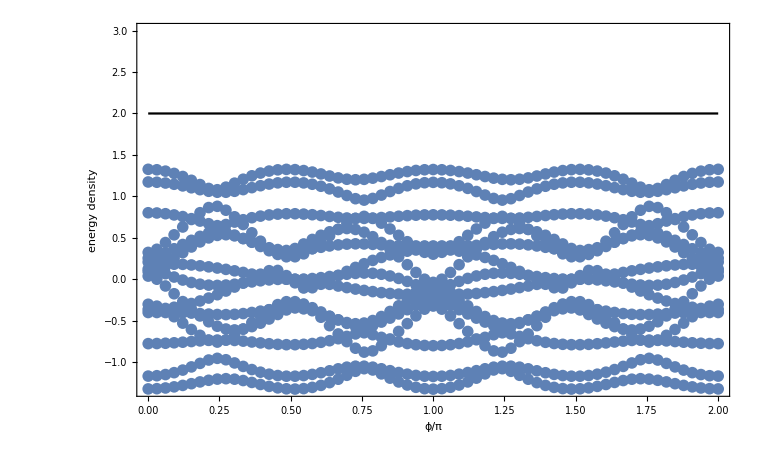

```mathematica
min=Min[Table[Length@ss,{ss,spectrum}]];
pmax=Max[Partition[Flatten[spectrum],2][[All,1]]];
pmin=Min[Partition[Flatten[spectrum],2][[All,1]]];
Show[Table[{ϕs,spectrum[[All,i,1]]}ᵀ//ListPlot,{i,min}],
ListPlot[{ϕs,spectrum[[All,2,2]]}ᵀ,PlotStyle->Black,Joined->True],(*Plot[Table[Re[J] Cos[π(x-2n/p)],{n,0,p-1}],{x,0,2},PlotStyle->Black],*)PlotRange->{pmin,3},GridLines->{Table[i/p,{i,2p}],{}},Frame->True,FrameLabel->{"ϕ/π","energy density"}]
```

```mathematica
HSQ = ⅇ^(ⅈ ϕ)(Γ[1].Γ[2]†+Γ[2].Δ[2]†);
HSQ += ⅇ^(ⅈ ϕ)(Δ[2].Δ[1]†+Δ[1].Γ[1]†);
HSQ=HSQ+HSQ†;
Eigenvalues[FullSimplify[HSQ,Assumptions->ϕ>0]]
```

{1/2 ⅇ^(-ⅈ ϕ) Root[-8-24 ⅇ^(2 ⅈ ϕ)-24 ⅇ^(4 ⅈ ϕ)-8 ⅇ^(6 ⅈ ϕ)-36 ⅇ^(2 ⅈ ϕ) #1+#1^3&,1],1/2 ⅇ^(-ⅈ ϕ) Root[-8-24 ⅇ^(2 ⅈ ϕ)-24 ⅇ^(4 ⅈ ϕ)-8 ⅇ^(6 ⅈ ϕ)-36 ⅇ^(2 ⅈ ϕ) #1+#1^3&,1],1/2 ⅇ^(-ⅈ ϕ) Root[-8-24 ⅇ^(2 ⅈ ϕ)-24 ⅇ^(4 ⅈ ϕ)-8 ⅇ^(6 ⅈ ϕ)-36 ⅇ^(2 ⅈ ϕ) #1+#1^3&,2],1/2 ⅇ^(-ⅈ ϕ) Root[-8-24 ⅇ^(2 ⅈ ϕ)-24 ⅇ^(4 ⅈ ϕ)-8 ⅇ^(6 ⅈ ϕ)-36 ⅇ^(2 ⅈ ϕ) #1+#1^3&,2],1/2 ⅇ^(-ⅈ ϕ) Root[-8-24 ⅇ^(2 ⅈ ϕ)-24 ⅇ^(4 ⅈ ϕ)-8 ⅇ^(6 ⅈ ϕ)-36 ⅇ^(2 ⅈ ϕ) #1+#1^3&,3],1/2 ⅇ^(-ⅈ ϕ) Root[-8-24 ⅇ^(2 ⅈ ϕ)-24 ⅇ^(4 ⅈ ϕ)-8 ⅇ^(6 ⅈ ϕ)-36 ⅇ^(2 ⅈ ϕ) #1+#1^3&,3],1/2 ⅇ^(-ⅈ ϕ) Root[-16 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2+16 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2-16 ⅇ^(4 ⅈ ϕ) Cos[ϕ]^2-16 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[ϕ]^2-32 ⅇ^(3 ⅈ ϕ) Cos[ϕ]^3+24 ⅈ ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-8 √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-24 ⅈ ⅇ^(4 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-8 √3 ⅇ^(4 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-16 √3 ⅇ^(3 ⅈ ϕ) Cos[ϕ]^2 Sin[ϕ]+24 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2-24 ⅈ √3 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2+24 ⅇ^(4 ⅈ ϕ) Sin[ϕ]^2+24 ⅈ √3 ⅇ^(4 ⅈ ϕ) Sin[ϕ]^2+480 ⅇ^(3 ⅈ ϕ) Cos[ϕ] Sin[ϕ]^2+48 √3 ⅇ^(3 ⅈ ϕ) Sin[ϕ]^3+(-2 ⅇ^(ⅈ ϕ) Cos[ϕ]+2 ⅈ √3 ⅇ^(ⅈ ϕ) Cos[ϕ]-2 ⅇ^(3 ⅈ ϕ) Cos[ϕ]-2 ⅈ √3 ⅇ^(3 ⅈ ϕ) Cos[ϕ]-68 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2-6 ⅈ ⅇ^(ⅈ ϕ) Sin[ϕ]+2 √3 ⅇ^(ⅈ ϕ) Sin[ϕ]+6 ⅈ ⅇ^(3 ⅈ ϕ) Sin[ϕ]+2 √3 ⅇ^(3 ⅈ ϕ) Sin[ϕ]-8 √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-60 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2) #1+#1^3&,1],1/2 ⅇ^(-ⅈ ϕ) Root[-16 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2+16 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2-16 ⅇ^(4 ⅈ ϕ) Cos[ϕ]^2-16 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[ϕ]^2-32 ⅇ^(3 ⅈ ϕ) Cos[ϕ]^3+24 ⅈ ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-8 √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-24 ⅈ ⅇ^(4 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-8 √3 ⅇ^(4 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-16 √3 ⅇ^(3 ⅈ ϕ) Cos[ϕ]^2 Sin[ϕ]+24 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2-24 ⅈ √3 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2+24 ⅇ^(4 ⅈ ϕ) Sin[ϕ]^2+24 ⅈ √3 ⅇ^(4 ⅈ ϕ) Sin[ϕ]^2+480 ⅇ^(3 ⅈ ϕ) Cos[ϕ] Sin[ϕ]^2+48 √3 ⅇ^(3 ⅈ ϕ) Sin[ϕ]^3+(-2 ⅇ^(ⅈ ϕ) Cos[ϕ]+2 ⅈ √3 ⅇ^(ⅈ ϕ) Cos[ϕ]-2 ⅇ^(3 ⅈ ϕ) Cos[ϕ]-2 ⅈ √3 ⅇ^(3 ⅈ ϕ) Cos[ϕ]-68 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2-6 ⅈ ⅇ^(ⅈ ϕ) Sin[ϕ]+2 √3 ⅇ^(ⅈ ϕ) Sin[ϕ]+6 ⅈ ⅇ^(3 ⅈ ϕ) Sin[ϕ]+2 √3 ⅇ^(3 ⅈ ϕ) Sin[ϕ]-8 √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-60 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2) #1+#1^3&,2],1/2 ⅇ^(-ⅈ ϕ) Root[-16 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2+16 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2-16 ⅇ^(4 ⅈ ϕ) Cos[ϕ]^2-16 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[ϕ]^2-32 ⅇ^(3 ⅈ ϕ) Cos[ϕ]^3+24 ⅈ ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-8 √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-24 ⅈ ⅇ^(4 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-8 √3 ⅇ^(4 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-16 √3 ⅇ^(3 ⅈ ϕ) Cos[ϕ]^2 Sin[ϕ]+24 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2-24 ⅈ √3 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2+24 ⅇ^(4 ⅈ ϕ) Sin[ϕ]^2+24 ⅈ √3 ⅇ^(4 ⅈ ϕ) Sin[ϕ]^2+480 ⅇ^(3 ⅈ ϕ) Cos[ϕ] Sin[ϕ]^2+48 √3 ⅇ^(3 ⅈ ϕ) Sin[ϕ]^3+(-2 ⅇ^(ⅈ ϕ) Cos[ϕ]+2 ⅈ √3 ⅇ^(ⅈ ϕ) Cos[ϕ]-2 ⅇ^(3 ⅈ ϕ) Cos[ϕ]-2 ⅈ √3 ⅇ^(3 ⅈ ϕ) Cos[ϕ]-68 ⅇ^(2 ⅈ ϕ) Cos[ϕ]^2-6 ⅈ ⅇ^(ⅈ ϕ) Sin[ϕ]+2 √3 ⅇ^(ⅈ ϕ) Sin[ϕ]+6 ⅈ ⅇ^(3 ⅈ ϕ) Sin[ϕ]+2 √3 ⅇ^(3 ⅈ ϕ) Sin[ϕ]-8 √3 ⅇ^(2 ⅈ ϕ) Cos[ϕ] Sin[ϕ]-60 ⅇ^(2 ⅈ ϕ) Sin[ϕ]^2) #1+#1^3&,3]}